# Dynamical System of anisotropic tachyon model

## Packages and call parallel kernels

```mathematica
<<MaTeX`
```

AbsoluteFileName::zfname: The file name cannot be an empty string.

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CloseKernels[];
```

```mathematica
LaunchKernels[];
```

## System

## Dynamical variables

## Density parameters

```mathematica
ΩDE:=y^2/(√(1-x^2))+z^2+Σ^2
```

```mathematica
Ωm:=1-ΩDE-Ωr
```

## Cosmological parameters

```mathematica
q:=1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)
```

```mathematica
wDE:=-1+2/3(3/2(x^2 y^2)/(√(1-x^2))+2 z^2+3 Σ^2)/(y^2/(√(1-x^2))+z^2+Σ^2)
```

```mathematica
weff:=wDE ΩDE+1/3 Ωr
```

## Dynamical analysis

## Autonomous set of equation

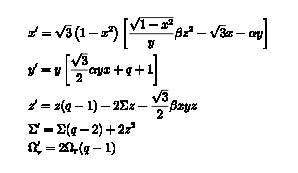

```mathematica
gx:=√3(1-x^2)((√(1-x^2))/y β z^2-√3 x-α y)
fx:=√3 β  z^2 √(1-x^2)-3x y-√3 α y^2
fy:=y((√3)/2 α y x+q+1)
fz:=z(q-1)-2Σ z-(√3)/2 β x y z
fS:=Σ(q-2)+2 z^2
fWr:=2Ωr(q-1)
```

#### Equations {x’,y’,z’,Σ’,Ωr’} under Transformation

```mathematica
Simplify[(-fx/.{x->-x,α->-α,β->-β})]
```

-3 x y-√3 y^2 α+√(3-3 x^2) z^2 β

```mathematica
(fy/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

y (1+q+1/2 √3 x y α)

```mathematica
(fz/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

(-1+q) z-1/2 √3 x y z β-2 z Σ

```mathematica
(fS/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

2 z^2+(-2+q) Σ

```mathematica
(fWr/.{x->-x,α->-α,β->-β,1/2(1+z^2+Ωr+3 Σ^2-3 √(1-x^2)y^2)->"q"})
```

2 (-1+q) Ωr

## Analytical dynamical analysis

```mathematica
Sol=Solve[{(fx/.√(1-x^2)->Γ)==0,(fy/.√(1-x^2)->Γ)==0,(fz/.√(1-x^2)->Γ)==0,(fS/.√(1-x^2)->Γ)==0,(fWr/.√(1-x^2)->Γ)==0},{x,y,z,Σ,Ωr}];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[Sol]
```

25

### Classification of fixed points

```mathematica
Sol[[1]]
```

{y→0,z→0,Σ→0,Ωr→1}

```mathematica
Sol[[3]]
```

{y→0,z→0,Σ→0,Ωr→1}

```mathematica
Limit[weff,Sol[[1]]]
```

1/3

```mathematica
Sol[[2]]
```

{y→0,z→0,Σ→-1,Ωr→0}

```mathematica
Sol[[5]]
```

{y→0,z→0,Σ→1,Ωr→0}

```mathematica
Limit[weff,Sol[[2]]]
```

1

```mathematica
Limit[weff,Sol[[5]]]
```

1

```mathematica
Sol[[4]]
```

{y→0,z→0,Σ→0,Ωr→0}

```mathematica
MaTeX["w_{\\text{eff}}",Magnification->1.3]
```

-Graphics-

```mathematica
Limit[weff,Sol[[4]]]
```

0

```mathematica
Sol[[6]]
```

{x→2/(√3),y→-2/α,z→0,Σ→0,Ωr→(α^2+12 Γ)/α^2}

```mathematica
Sol[[7]]
```

{x→-2/(√3),y→2/α,z→0,Σ→0,Ωr→(α^2+12 Γ)/α^2}

```mathematica
Sol[[8]]
```

{x→√2,y→-(√6)/α,z→0,Σ→-(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
Sol[[9]]
```

{x→√2,y→-(√6)/α,z→0,Σ→(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
Sol[[10]]
```

{x→-√2,y→(√6)/α,z→0,Σ→-(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
Sol[[11]]
```

{x→-√2,y→(√6)/α,z→0,Σ→(√(α^2+6 Γ))/α,Ωr→0}

```mathematica
√(1-x^2)/.x^2->4/3
```

ⅈ/(√3)

```mathematica
√(1-x^2)/.x^2->2
```

ⅈ

```mathematica
Sol[[12]]
```

{x→α/(√(α^2+3 Γ)),y→-(√3)/(√(α^2+3 Γ)),z→0,Σ→0,Ωr→0}

```mathematica
Sol[[13]]
```

{x→-α/(√(α^2+3 Γ)),y→(√3)/(√(α^2+3 Γ)),z→0,Σ→0,Ωr→0}

```mathematica
{fx,fy,fz,fWr,fS}/.{Ωr->0,Σ->0,z->0}
```

{-3 x y-√3 y^2 α,y (1+1/2 (1-3 √(1-x^2) y^2)+1/2 √3 x y α),0,0,0}

```mathematica
Solve[{(fx/.{Ωr->0,Σ->0,z->0})==0,(fy/.{Ωr->0,Σ->0,z->0})==0},{x,y}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0},{x→-1,y→(√3)/α},{x→1,y→-(√3)/α},{x→-(α √(-α^2-√(36+α^4)))/(3 √2),y→(√(-α^2-√(36+α^4)))/(√6)},{x→(α √(-α^2-√(36+α^4)))/(3 √2),y→-(√(-α^2-√(36+α^4)))/(√6)},{x→-(α √(-α^2+√(36+α^4)))/(3 √2),y→(√(-α^2+√(36+α^4)))/(√6)},{x→(α √(-α^2+√(36+α^4)))/(3 √2),y→-(√(-α^2+√(36+α^4)))/(√6)}}

```mathematica
Sol[[14]]
```

{x→(4 √2 √(8+β^2 Γ))/(8 √3+√3 β^2 Γ),y→-(√(8+β^2 Γ))/(√2 α),z→-(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Sol[[15]]
```

{x→(4 √2 √(8+β^2 Γ))/(8 √3+√3 β^2 Γ),y→-(√(8+β^2 Γ))/(√2 α),z→(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Sol[[16]]
```

{x→(4 √2 √(8+β^2 Γ))/(-8 √3-√3 β^2 Γ),y→(√(8+β^2 Γ))/(√2 α),z→-(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Sol[[17]]
```

{x→(4 √2 √(8+β^2 Γ))/(-8 √3-√3 β^2 Γ),y→(√(8+β^2 Γ))/(√2 α),z→(√β)/(√2 √α),Σ→β/α,Ωr→(2 α^2-α β-6 β^2+24 Γ+3 β^2 Γ^2)/(2 α^2)}

```mathematica
Simplify[((4 √2 √(8+β^2 Γ))/(8 √3+√3 β^2 Γ))^2,{Γ>0,β∈Reals}]
```

32/(24+3 β^2 Γ)

```mathematica
Solx2=Solve[χ==32/(24+3 β^2 √(1-χ)),χ]/.χ->x^2
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x^2→(-64+β^4)/(3 β^4)-(-331776-31104 β^4-81 β^8)/(243 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))+((-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(3 β^4)},{x^2→(-64+β^4)/(3 β^4)+((1+ⅈ √3) (-331776-31104 β^4-81 β^8))/(486 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))-((1-ⅈ √3) (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(6 β^4)},{x^2→(-64+β^4)/(3 β^4)+((1-ⅈ √3) (-331776-31104 β^4-81 β^8))/(486 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))-((1+ⅈ √3) (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(6 β^4)}}

```mathematica
Solx2[[1,1]]
```

x^2→(-64+β^4)/(3 β^4)-(-331776-31104 β^4-81 β^8)/(243 β^4 (-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))+((-262144-36864 β^4-960 β^8+β^12+32 √(4096 β^12+384 β^16-3 β^20))^(1/3))/(3 β^4)

```mathematica
Reduce[(Solx2[[1,1,2]]>0)&&(4096 β^12+384 β^16-3 β^20>0),β]
```

False

```mathematica
Sol[[18]]
```

{x→(58+1)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→-√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/(16 α^5+64 α^4 β+84 α^3 β^2+4+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(108 α β^2)/1+14+1/(2 1)+(81 β^5 Γ^3)/(2 (16 α^5+7+1))-(√((-240 α^3-504 α^2 β-216 α β^2-384 α Γ-576 β Γ+12+39 α^3 β^2 Γ^3-63 α^2 β^3 Γ^3-135 α β^4 Γ^3-81 β^5 Γ^3)^2-4 (576 α+9+1) (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4))),1,Σ→1,Ωr→0}
 |  |  |  |

```mathematica
Sol[[19]]
```

{x→(58+1)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→-√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/(16 α^5+64 α^4 β+84 α^3 β^2+4+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(108 α β^2)/1+14+1/(2 1)+(81 β^5 Γ^3)/(2 (16 α^5+7+1))-(√((-240 α^3-504 α^2 β-216 α β^2-384 α Γ-576 β Γ+12+39 α^3 β^2 Γ^3-63 α^2 β^3 Γ^3-135 α β^4 Γ^3-81 β^5 Γ^3)^2-4 (576 α+9+1) (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4))),z→1,Σ→1,Ωr→0}
 |  |  |  |

```mathematica
Sol[[20]]
```

{x→(3072 √3 α^3 √((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+16+(81 β^5 Γ^3)/(2 1)-(√((1)^2-4 1 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+1+120 2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))+47)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+19),z→-1,Σ→(16 α+79+1/1)/(-16 α-24 β+1-12 α 1 Γ-9 β^3 Γ),Ωr→0}
 |  |  |  |

```mathematica
Sol[[21]]
```

{x→(3072 √3 α^3 √((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+16+(81 β^5 Γ^3)/(2 1)-(√((1)^2-4 1 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+1+120 2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))+47)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+19),z→1,Σ→(16 α+79+1/1)/(-16 α-24 β+1-12 α 1 Γ-9 β^3 Γ),Ωr→0}
 |  |  |  |

```mathematica
Sol[[22]]
```

{x→(58+1)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→-√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/(16 α^5+64 α^4 β+84 α^3 β^2+4+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(108 α β^2)/1+14+1/(2 1)+(81 β^5 Γ^3)/(2 (16 α^5+7+1))+(√((-240 α^3-504 α^2 β-216 α β^2-384 α Γ-576 β Γ+12+39 α^3 β^2 Γ^3-63 α^2 β^3 Γ^3-135 α β^4 Γ^3-81 β^5 Γ^3)^2-4 (576 α+9+1) (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4))),1,Σ→1,Ωr→0}
 |  |  |  |

```mathematica
Sol[[23]]
```

{x→(58+1)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→-√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/(16 α^5+64 α^4 β+84 α^3 β^2+4+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(108 α β^2)/1+14+1/(2 1)+(81 β^5 Γ^3)/(2 (16 α^5+7+1))+(√((-240 α^3-504 α^2 β-216 α β^2-384 α Γ-576 β Γ+12+39 α^3 β^2 Γ^3-63 α^2 β^3 Γ^3-135 α β^4 Γ^3-81 β^5 Γ^3)^2-4 (576 α+9+1) (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4))),z→1,Σ→1,Ωr→0}
 |  |  |  |

```mathematica
Sol[[24]]
```

{x→(3072 √3 α^3 √((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+16+(81 β^5 Γ^3)/(2 1)+(√((1)^2-4 1 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+1+120 2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))+47)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+17+(√((1)^2-4 (1) (1)))/(2 (16 α^5+7+36 α^2 β^3 Γ^4))),z→1,Σ→1/1,Ωr→0}
 |  |  |  |

```mathematica
Sol[[25]]
```

{x→(3072 √3 α^3 √((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+16+(81 β^5 Γ^3)/(2 1)+(√((1)^2-4 1 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+1+120 2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))/(2 (16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)))+47)/(-9216 α^2-27648 α β-20736 β^2+5760 α^3 β Γ-5184 α^2 β^2 Γ-31104 α β^3 Γ-15552 β^4 Γ-1044 α^4 β^2 Γ^2+4824 α^3 β^3 Γ^2-1296 α^2 β^4 Γ^2-9720 α β^5 Γ^2-4860 β^6 Γ^2+45 α^5 β^3 Γ^3-333 α^4 β^4 Γ^3+594 α^3 β^5 Γ^3+486 α^2 β^6 Γ^3-1215 α β^7 Γ^3-729 β^8 Γ^3),y→√((120 α^3)/(16 α^5+64 α^4 β+84 α^3 β^2+36 α^2 β^3+48 α^4 β Γ^2+120 α^3 β^2 Γ^2+72 α^2 β^3 Γ^2+36 α^3 β^2 Γ^4+36 α^2 β^3 Γ^4)+(252 α^2 β)/1+17+(√((1)^2-4 (1) (1)))/(2 (16 α^5+7+36 α^2 β^3 Γ^4))),z→1,Σ→1/1,Ωr→0}
 |  |  |  |

### Fixed points

### Numerical dynamical analysis

#### Generating numerical region

```mathematica
n=50000;
```

```mathematica
v:=ImplicitRegion[-30<=α<=30&&0<=β<=30,{α,β}]
```

```mathematica
c1=(α<0&&β<-α/3-2/3 √((36+α^4)/α^2))||(α>0&&β>-α/3+2/3 √((36+α^4)/α^2));
```

```mathematica
v2:=ImplicitRegion[c1,{{α,-30,30},{β,0,30}}];
```

```mathematica
Solutions = {};
```

```mathematica
(*SetSharedVariable[Solutions];
ParallelDo[
            
            {a, b} = RandomPoint[v];
            NSol = NSolve[
                        {
                              (fx /. {α -> a, β -> b, Ωr -> 0}) == 0,
                              (fy /. {α -> a, β -> b, Ωr -> 0}) == 0,
                              (fz /. {α -> a, β -> b, Ωr -> 0}) == 0,
                              (fS /. {α -> a, β -> b, Ωr -> 0}) == 0,
                              -1 < x < 1, -1 <= Σ <= 1, -1 <= z <= 1, Σ != 0}, {x, y, Σ, z}, Reals];
            AppendTo[Solutions, {{a, b}, NSol}];
            , {i, 1, n}] // AbsoluteTiming
Export["NumericalData/FixedPointSolutions.dat", Solutions, "CSV”,OverwriteTarget->”KeepBoth”];
*)
```

```mathematica
Solutions = If[Solutions=={},Import["NumericalData/FixedPointSolutions.dat", "CSV"]//ToExpression,Solutions];
n=Length[Solutions];
```

```mathematica
Viable={};
SolViable={};
NoViable={};
```

```mathematica
(*Do[
    If[
      Solutions[[i, 2]] != {} && AnyTrue[Table[(Ωm /. Ωr -> 0 /. Solutions[[i, 2, j]]), {j, 1, Length[Solutions[[i, 2]]]}], # >= 0 &],
      AppendTo[Viable, Solutions[[i, 1]]];
      AppendTo[SolViable, Solutions[[i, 2]]];,
      AppendTo[NoViable, Solutions[[i, 1]]];
      ]
    , {i, 1, n}] // AbsoluteTiming
Export["NumericalData/ClassificationOfFixedPoints/Viable.dat", Viable, "CSV", OverwriteTarget -> "KeepBoth"];
Export["NumericalData/ClassificationOfFixedPoints/NoViable.dat", NoViable, "CSV", OverwriteTarget -> "KeepBoth"];
Export["NumericalData/ClassificationOfFixedPoints/SolViable.dat", SolViable, "CSV", OverwriteTarget -> "KeepBoth"];

*)
```

```mathematica
Viable=If[Viable=={},Import["NumericalData/ClassificationOfFixedPoints/Viable.dat","CSV"],Viable];
NoViable=If[NoViable=={},Import["NumericalData/ClassificationOfFixedPoints/NoViable.dat","CSV"],NoViable];
SolViable=If[SolViable=={},Import["NumericalData/ClassificationOfFixedPoints/SolViable.dat","CSV"]//ToExpression,SolViable];
```

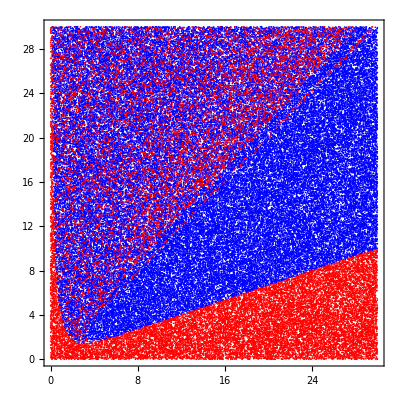

```mathematica
ListPlot[{Viable,NoViable},AspectRatio->1,PlotRange->{{0,30},{0,30}},Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->{Blue,Red},PlotLegends->{MaTeX["\\text{Viables}",Magnification->1.3],MaTeX["\\text{No viables}",Magnification->1.3]},Axes->False]
```

#### Analytical approximation of the region

```mathematica
weffMin=Table[{Viable[[i,1]],Viable[[i,2]],(weff/.Ωr->0/.SolViable[[i]])//Min},{i,1,Length[SolViable]}];
```

```mathematica
m=200;
maxA=Max[Viable[[All,1]]];
maxB=Max[Viable[[All,2]]];
```

```mathematica
GridOfRegioneff=Table[{Ceiling[maxA] i/m,Ceiling[maxB]},{i,1,m}];
Do[
If[
GridOfRegioneff[[Ceiling[Viable[[i,1]] m/maxA],2]]>Viable[[i,2]]&&weffMin[[i,3]]<-1/3,
GridOfRegioneff[[Ceiling[Viable[[i,1]] m/maxA],2]]=Viable[[i,2]]
]
,{i,1,Length[Viable]}];
```

```mathematica
BoundaryOfRegioneff=DeleteCases[GridOfRegioneff,{_,Ceiling[maxB]}];
```

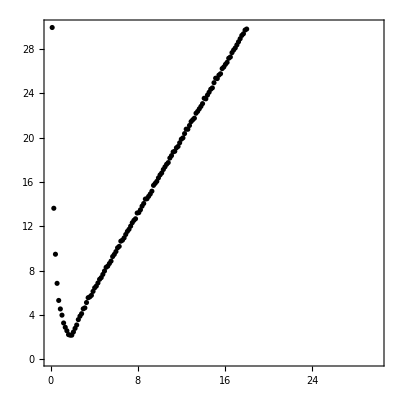

```mathematica
ListPlot[BoundaryOfRegioneff,AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->Black,Axes->False,PlotRange->{{0,30},{0,30}}]
```

```mathematica
fit2=LinearModelFit[BoundaryOfRegioneff,{1/α^4,1/α^3,1/α^2,1/α,1,α},α]
```

FittedModel[0.317674+0.212096/α^4-2.48435/α^3+8.53325/α^2-4.9116/α+1.65652 α]

```mathematica
fit2["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
1/α^3 | 1 | -27471.8 | -27471.8 | -591112. | -1.36672×10^-213
1/α^2 | 1 | 405.658 | 405.658 | 8728.54 | 1.45882×10^-109
1/α | 1 | 10879. | 10879. | 234084. | 1.12197×10^-190
1 | 1 | 22739.2 | 22739.2 | 489278. | 6.3929×10^-209
α | 1 | 1819.98 | 1819.98 | 39160.5 | 1.78825×10^-146
Error | 114 | 5.29814 | 0.0464749 |  | 
Total | 119 | 8377.27 |  |  |

```mathematica
MaTeX["\\text{The linear approximation is}",Magnification->1.3]
```

-Graphics-

```mathematica
LinearFitAccelerated=LinearModelFit[
DeleteCases[Table[
If[BoundaryOfRegion[[i,1]]>5,
BoundaryOfRegioneff[[i]]]

,{i,1,Length[BoundaryOfRegioneff]}],Null]
,{1,α},α]
```

FittedModel[-0.321655+1.67887 α]

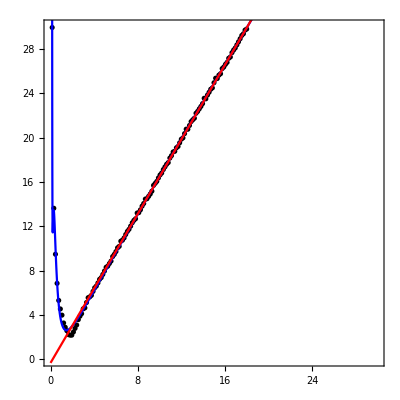

```mathematica
Show[
ListPlot[BoundaryOfRegioneff,AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->Black,Axes->False,PlotRange->{{0,30},{0,30}}],
Plot[{fit2[α],LinearFitAccelerated[α]},{α,0,30},PlotStyle->{Blue,Red},PlotLegends->LineLegend[{Directive[Dotted,Black],Directive[Thick,Blue],Directive[Thick,Red]},{MaTeX["\\text{Boundary}",Magnification->1.3],MaTeX["\\text{Fit}",Magnification->1.3],MaTeX["\\text{Linear fit}",Magnification->1.3]}]]
]
```

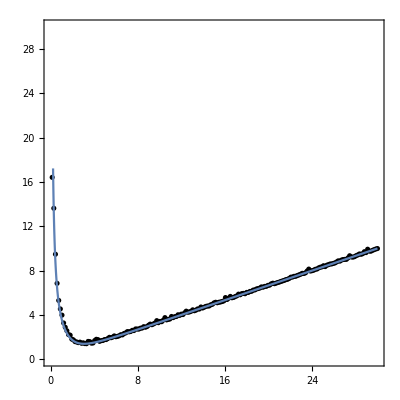

```mathematica
Show[
ListPlot[BoundaryOfRegion,AspectRatio->1,Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->Black,Axes->False,PlotRange->{{0,30},{0,30}}],
Plot[-α/3+2/3 √((36+α^4)/α^2),{α,0,30},PlotLegends->LineLegend[{Directive[Dotted,Black],Directive[Thick,Blue]},{MaTeX["\\text{Boundary}",Magnification->1.3],MaTeX["\\text{Fit}",Magnification->1.3]}]]
]
```

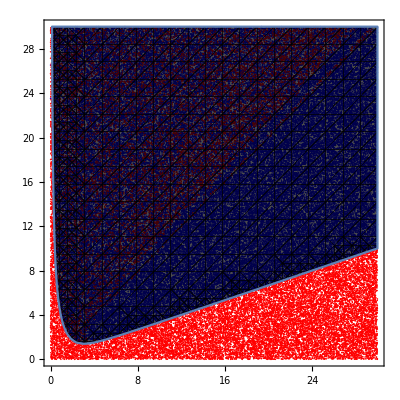

```mathematica
Show[
ListPlot[{Viable,NoViable},AspectRatio->1,PlotRange->{{0,30},{0,30}},Frame->True,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotStyle->{Blue,Red},PlotLegends->{MaTeX["\\text{Viables}",Magnification->1.3],MaTeX["\\text{No viables}",Magnification->1.3]},Axes->False]
,
RegionPlot[β>-α/3+2/3 √((36+α^4)/α^2),{α,0,30},{β,0,30},PlotStyle->Directive[Black,Opacity[0.7]]]
]
```

```mathematica
fitAnalitical[α_]=-α/3+2/3 √((36+α^4)/α^2);
```

```mathematica
Nin2=ParallelSum[UnitStep[Viable[[n,2]]-fitAnalitical[Viable[[n,1]]]],{n,1,Length[Viable]}];
Nout2=ParallelSum[UnitStep[-Viable[[n,2]]+fitAnalitical[Viable[[n,1]]]],{n,1,Length[Viable]}];
```

```mathematica
ErrorFit2=Nout2/(Nin2+Nout2)//N//ScientificForm
```

4.09093×10^-5

```mathematica
Viable=Import["NumericalData/ClassificationOfFixedPointsCorrection/Viable.dat","CSV"];
NoViable=Import["NumericalData/ClassificationOfFixedPointsCorrection/NoViable.dat","CSV"];
SolViable=Import["NumericalData/ClassificationOfFixedPointsCorrection/SolViable.dat","CSV"]//ToExpression;
```

```mathematica
SolViable=DeleteCases[SolViable,{_,{}}];
```

### Fixed points classified

```mathematica
L:={Ωr,Ωm,ΩDE}
```

#### Radiation point

```mathematica
L/.{y->0,z->0,Σ->0,Ωr->1}
```

{1,0,0}

```mathematica
Limit[weff,{x->0,y->0,Ωr->1,Σ->0,z->0}]
```

1/3

#### Matter point

```mathematica
L/.{y->0,z->0,Σ->0,Ωr->0}
```

{0,1,0}

```mathematica
Limit[weff,{x->0,y->0,Ωr->0,Σ->0,z->0}]
```

0

#### Isotropic DE point

```mathematica
FullSimplify[L/.{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0},α∈Reals]
```

{0,1+(α^2-√(36+α^4))/(√2 √(18+α^4-α^2 √(36+α^4))),(-α^2+√(36+α^4))/(√2 √(18+α^4-α^2 √(36+α^4)))}

```mathematica
√Simplify[(Expand@((α^2-√(36+α^4))^2))/2]
```

√(18+α^4-α^2 √(36+α^4))

```mathematica
(L/.{x->(α √(-α^2+√(36+α^4)))/(3 √2),y->-(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}//FullSimplify)/.α^2-√(36+α^4)->-√2 √(18+α^4-α^2 √(36+α^4))
```

{0,0,(-α^2+√(36+α^4))/(√2 √(18+α^4-α^2 √(36+α^4)))}

```mathematica
Limit[weff,{x->(α √(-α^2+√(36+α^4)))/(3 √2),y->-(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]
```

1/6 (α^2-√(36+α^4)) √(1-1/18 α^2 (-α^2+√(36+α^4)))

```mathematica
Limit[weff,{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]
```

1/6 (α^2-√(36+α^4)) √(1-1/18 α^2 (-α^2+√(36+α^4)))

```mathematica
Limit[wDE,{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]
```

-1+1/18 α^2 (-α^2+√(36+α^4))

```mathematica
Reduce[Limit[weff,{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),z->0,Σ->0,Ωr->0}]<-1/3]
```

-√2 3^(1/4)<α<√2 3^(1/4)

#### Anisotropic DE point

```mathematica
weffMin=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Min[(weff/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];
wDEMin=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Min[(wDE/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];
WmMin=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Min[(Ωm/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];
weffMax=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Max[(weff/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];
wDEMax=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Max[(wDE/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];
WmMax=Table[{SolViable[[i,1,1]],SolViable[[i,1,2]],Max[(Ωm/.Ωr->0/.SolViable[[i,2]])]},{i,1,Length[SolViable]}];
```

```mathematica
weffgr=Show[
ListContourPlot[{weffMin},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["w_{\\rm eff}" ]],Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}},ColorFunction->"TemperatureMap",LabelStyle->{Black,15}]
]
```

```mathematica
Export["FixedPoints/weff.pdf",weffgr];
```

```mathematica
wDEgr=Show[
ListContourPlot[{wDEMin},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["w_{\\rm DE}" ]],Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}},ColorFunction->"TemperatureMap",LabelStyle->{Black,15}]
]
```

```mathematica
Export["FixedPoints/wDE.pdf",wDEgr];
```

```mathematica
Wmgr=Show[
ListContourPlot[{WmMax},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\Omega_m" ]],Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}},ColorFunction->"TemperatureMap",LabelStyle->{Black,15}]
]
```

```mathematica
Export["FixedPoints/Wm.pdf",Wmgr];
```

```mathematica
weffAtractive=DeleteCases[
Table[
If[
Min[weffMin[[i,3]]<-1/3],
weffMin[[i]]
],{i,1,Length[weffMin]}
]
,Null];
WmAtractive=DeleteCases[
Table[
If[
Min[weffMin[[i,3]]<-1/3],
WmMax[[i]]
],{i,1,Length[weffMin]}
]
,Null];
```

```mathematica
WmAtractivegr=Show[ListContourPlot[{WmAtractive},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\Omega_m"]],Right],ColorFunction->"TemperatureMap",AspectRatio->1,PlotRange->{{0,30},{0,30}},FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]}],RegionPlot[(α>0&&β>-α/3+2/3 √((36+α^4)/α^2)),{α,0,30},{β,0,30},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotLegends->Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-2) without accelerated expansion}"],40°],{0.55,0.45}],FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.1], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]]
```

```mathematica
weffAtractgr=Show[ListContourPlot[{weffAtractive},Frame->True,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["w_{\\text{DE}}\\simeq w_{\\text{eff}}"]],Right],ColorFunction->"TemperatureMap",AspectRatio->1,PlotRange->{{0,30},{0,30}},FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]}],RegionPlot[(α>0&&β>-α/3+2/3 √((36+α^4)/α^2)),{α,0,30},{β,0,30},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},LabelStyle->{Black,15},PlotLegends->Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-2) without accelerated expansion}"],40°],{0.55,0.45}],FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.1], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]]
```

-Graphics-

```mathematica
Export["FixedPoints/WeffAttractive.pdf",weffAtractgr];
```

## Stability analysis

```mathematica
system:={gx,fy,fz,fS,fWr}
```

## Radiation points

```mathematica
Pr=Limit[D[system,{{x,y,z,Σ,Ωr}}],{y->0,Ωr->1,Σ->0,z->0}];
```

```mathematica
Pr//MatrixForm
```

(-3+9 x^2 | √3 (-1+x^2) α | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Simplify[Eigensystem[Pr]]
```

{{2,-1,1,0,-3+9 x^2},{{-(√3 (-1+x^2) α)/(-5+9 x^2),1,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,1,0,0},{1,0,0,0,0}}}

## Matter points

```mathematica
Pm=Limit[D[system,{{x,y,z,Σ,Ωr}}],{y->0,Ωr->0,Σ->0,z->0}];
```

```mathematica
Pm//MatrixForm
```

(-3+9 x^2 | √3 (-1+x^2) α | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | -3/2 | 0
0 | 0 | 0 | 0 | -1)

```mathematica
Simplify[Eigensystem[Pm]]
```

{{-3/2,3/2,-1,-1/2,-3+9 x^2},{{0,0,0,1,0},{-(2 (-1+x^2) α)/(3 √3 (-1+2 x^2)),1,0,0,0},{0,0,0,0,1},{0,0,1,0,0},{1,0,0,0,0}}}

## DE points

### Isotropic DE

```mathematica
PDEI=FullSimplify[Limit[D[system,{{x,y,z,Σ,Ωr}}],{x->-(α √(-α^2+√(36+α^4)))/(3 √2),y->(√(-α^2+√(36+α^4)))/(√6),Ωr->0,Σ->0,z->0}]];
```

```mathematica
DEIEigenSystem=Simplify[Eigensystem[PDEI]];
```

```mathematica
PDEI2=FullSimplify[Limit[D[system,{{x,y,Ωr,z,Σ}}],{x->(α √(-α^2+√(36+α^4)))/(3 √2),y->-(√(-α^2+√(36+α^4)))/(√6),Ωr->0,Σ->0,z->0}]];
```

```mathematica
Evaluate[PDEI2[[1]]==PDEI[[1]]]
```

True

```mathematica
EigenvaluesDEI=Plot[{DEIEigenSystem[[1,1]],DEIEigenSystem[[1,2]],DEIEigenSystem[[1,3]],DEIEigenSystem[[1,4]]},{α,-√2 3^(1/4),√2 3^(1/4)},Frame->True,PlotLegends->Placed[
LineLegend[{(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_1"],(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_{2}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_{3}"],(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_4"]},LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->Framed]
,{0.5,0.8}],Axes->False,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]
```

-Graphics-

```mathematica
Export["FixedPoints/EigenvaluesDEI.pdf",EigenvaluesDEI];
```

```mathematica
EigenvalueDEIl5=ContourPlot[DEIEigenSystem[[1,5]],{α,-30,30},{β,-30,30},PlotPoints->40,FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_5"]],Right],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
EigenvalueDEIl5=ContourPlot[DEIEigenSystem[[1,5]],{α,-√2 3^(1/4),√2 3^(1/4)},{β,-30,30},PlotPoints->40,FrameStyle->Directive[Black,Thickness[0.0028]],LabelStyle->{Black,15}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\lambda_5"]],Right],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
Export["FixedPoints/EigenValuel5DEI.pdf",EigenvalueDEIl5];
```

```mathematica
Reduce[{DEIEigenSystem[[1,5]]<0},{α,β}]
```

β∈ℝ&&((α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β<-α/3+2/3 √((36+α^4)/α^2)))

```mathematica
MaTeX["\\text{it is the region where the isotropic solutions is an attractor and produce accelerate expansion, i. e. there are isotropic DE.}",Magnification->1.3]
```

-Graphics-

```mathematica
Reduce[{DEIEigenSystem[[1,5]]<0,-√2 3^(1/4)<α<√2 3^(1/4)},{α,β}]
```

β∈ℝ&&((-√2 3^(1/4)<α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(0<α<√2 3^(1/4)&&β<-α/3+2/3 √((36+α^4)/α^2)))

```mathematica
RegionPlot[{(α>0&&β<-α/3+2/3 √((36+α^4)/α^2))||α==0||(α<0&&β>-α/3-2/3 √((36+α^4)/α^2))},{α,-30,30},{β,-30,30},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.52],PlotStyle->RGBColor[0.22,0.58,0.46], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]
```

-Graphics-

```mathematica
RegionPrev=Show[
RegionPlot[
(α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β<-α/3+2/3 √((36+α^4)/α^2)),{α,-10,10},{β,-15,15},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotLegends->{Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{Attractive}"],-45°],{0.25,0.75}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{zone}"],-45°],{0.5,0.5}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{``(DE-1)''}"],-45°],{0.75,0.25}]},PlotStyle->RGBColor[0.22,0.58,0.46,0.9], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},Epilog->{Directive[RGBColor[0.92,0.77,0.32],Dashed,Thick],Line[{{√2 3^(1/4),-15},{√2 3^(1/4),(-(√2 3^(1/4))/3+2/3 √((36+(√2 3^(1/4))^4)/((√2 3^(1/4))^2)))}}],Line[{{-√2 3^(1/4),15},{-√2 3^(1/4),(-(-√2 3^(1/4))/3-2/3 √((36+(-√2 3^(1/4))^4)/((-√2 3^(1/4))^2)))}}]}
],RegionPlot[{(α>0&&β>fit1[α]),(α<0&&-β>fit1[-α])},
{α,-10,10},{β,-15,15},LabelStyle->{Black,15},PlotLegends->{Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{``(DE-2)''}"],45°],{0.75,0.75}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{``(DE-2)''}"],45°],{0.25,0.25}]},FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.6], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}, Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]
]
```

-Graphics-

```mathematica
Export["FixedPoints/PremilinaryRegion.pdf",RegionPrev];
```

```mathematica
ClasifyRegion=Show[RegionPlot[(α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β<-α/3+2/3 √((36+α^4)/α^2)),{α,-10,10},{β,-15,15},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotLegends->{Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-1)}"],π/2],{0.5,0.5}],Placed[Rotate[(MaTeX[#,Magnification->.8]&)/@Style["\\text{(DE-1) and (DE-2)}"],π/2],{0.56,0.82}],Placed[Rotate[(MaTeX[#,Magnification->.8]&)/@Style["\\text{(DE-1) and (DE-2)}"],π/2],{0.44,0.17}]},PlotStyle->RGBColor[0.22,0.58,0.46], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]},Epilog->{{Directive[RGBColor[0.92,0.77,0.32],Dashed,Thick],Line[{{√2 3^(1/4),-15},{√2 3^(1/4),(-(√2 3^(1/4))/3+2/3 √((36+(√2 3^(1/4))^4)/((√2 3^(1/4))^2)))}}],Line[{{-√2 3^(1/4),15},{-√2 3^(1/4),(-(-√2 3^(1/4))/3-2/3 √((36+(-√2 3^(1/4))^4)/((-√2 3^(1/4))^2)))}}]},{Directive[RGBColor[1,0.06,0.13],Dashed,Thick],Line[{{√2 3^(1/4),15},{√2 3^(1/4),(-(√2 3^(1/4))/3+2/3 √((36+(√2 3^(1/4))^4)/((√2 3^(1/4))^2)))}}],Line[{{-√2 3^(1/4),-15},{-√2 3^(1/4),(-(-√2 3^(1/4))/3-2/3 √((36+(-√2 3^(1/4))^4)/((-√2 3^(1/4))^2)))}}]}}],RegionPlot[{(α<0&&β<-α/3-2/3 √((36+α^4)/α^2))||(α>0&&β>-α/3+2/3 √((36+α^4)/α^2))},
{α,-10,10},{β,-15,15},LabelStyle->{Black,15},PlotLegends->{Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-2)}"],63°],{0.67,0.86}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{(DE-2)}"],75°],{0.33,0.12}]},FrameStyle->Directive[Black,Thickness[0.0028]],PlotStyle->RGBColor[0.95,0.63,0.12,0.52], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {1, 0}, {1, 1}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}],Plot[{If[(α>0&&LinearFitAccelerated[α]>-α/3+2/3 √((36+α^4)/α^2)&&LinearFitAccelerated[α]<15),LinearFitAccelerated[α]],If[(α<0&&LinearFitAccelerated[α]<-α/3-2/3 √((36+α^4)/α^2)&&LinearFitAccelerated[α]>-15),LinearFitAccelerated[α]]},{α,-10,10},PlotStyle->Directive[RGBColor[0.25,0.5,0.49],Dashed],PlotLegends->{Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{No accelated}"],0],{0.8,0.3}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{No accelated}"],0],{0.2,0.75}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{No accelated}"],45°],{0.8,0.75}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\text{No accelated}"],45°],{0.2,0.25}]}], Prolog -> {Opacity[0], Texture[{{{0, 0, 0, 0}}}], 
    VertexTextureCoordinates -> {{0, 0}, {2, 0}, {2, 2}}, 
    Polygon[{{0, 0}, {.1, 0}, {.1, .1}}]}]
```

-Graphics-

```mathematica
Export["FixedPoints/ClasifyRegion.pdf",ClasifyRegion];
```

### Anisotric DE

#### Stability Calculus

```mathematica
JacobianMaTrix={};
```

```mathematica
JM=(D[system, {{x, y, z, Σ, Ωr}}]/.Ωr->0);
```

```mathematica
(*JacobianMaTrix = Table[
                    Table[
                         Limit[
                              (JM /. { α -> SolViable[[n, 1, 1]], β -> SolViable[[n, 1, 2]]})
                              , SolViable[[n, 2, j]]]
                         , {j, 1, Length[SolViable[[n, 2]]]}
                        ]
                       , {n, 1, Length[SolViable]}]; // AbsoluteTiming
Export["Stability/JacobianMaTriX.dat", JacobianMaTrix, "CSV", OverwriteTarget -> "KeepBoth"];*)
```

{16387.5,Null}

```mathematica
JacobianMaTrix=If[JacobianMaTrix=={},Import["Stability/JacobianMaTriX.dat","CSV"],JacobianMaTrix]//ToExpression;
```

```mathematica
EigenSystem=Table[
       Table[
         Eigensystem[JacobianMaTrix[[j, i]]], {i, 1, Length[JacobianMaTrix[[j]]]}
         ]
        , {j, 1 , Length[JacobianMaTrix]}]; // AbsoluteTiming
```

{8.40879,Null}

```mathematica
Export["Stability/EygenSystem.dat", EigenSystem, "CSV"];
```

```mathematica
SolNoViable=Import["NumericalData/ClassificationOfFixedPointsCorrection/SolNoViable.dat","CSV"]//ToExpression;
```

```mathematica
SolNoViable=DeleteCases[SolNoViable,{_,{}}];
```

```mathematica
JacobianMaTrixNoViable={};
```

```mathematica
(*JacobianMaTrixNoViable = ParallelTable[
                                    Table[
                                             Limit[
                                                      (JM /. { α -> SolNoViable[[n, 1, 1]], β -> SolNoViable[[n, 1, 2]]})
                                                      , SolNoViable[[n, 2, j]]]
                                             , {j, 1, Length[SolNoViable[[n, 2]]]}
                                            ]
                                       , {n, 1, Length[SolNoViable]}]; // AbsoluteTiming
Export["Stability/JacobianMaTriXNoViable.dat", JacobianMaTrixNoViable, "CSV", OverwriteTarget -> "KeepBoth"];*)
```

```mathematica
JacobianMaTrixNoViable=If[JacobianMaTrixNoViable=={},Import["Stability/JacobianMaTriXNoViable.dat","CSV"],JacobianMaTrixNoViable]//ToExpression;
```

```mathematica
EigenSystemNoViable=Table[
       DeleteCases[Table[
If[MatrixQ[JacobianMaTrixNoViable[[j,i]],NumberQ],
         Eigensystem[JacobianMaTrixNoViable[[j, i]]] ]
, {i, 1, Length[JacobianMaTrixNoViable[[j]]]}
         
],Null]
        , {j, 1 , Length[JacobianMaTrixNoViable]}]; // AbsoluteTiming
Export["Stability/EygenSystemNoViable.dat", EigenSystemNoViable, "CSV"];
```

{8.80508,Null}

#### Sign of eigen values depending on α and β values

```mathematica
l1 = {};
l2 = {};
l3 = {};
l4 = {};
l5 = {};
```

```mathematica
Do[
  np = 1;
  While[np<=Length[EigenSystem[[i]]]&&AnyTrue[Sign[Re[EigenSystem[[i, np, 1]]]], # > 0 &], np++;];
If[np>Length[EigenSystem],np--;];
  AppendTo[
   l1, {SolViable[[i,1, 1]], SolViable[[i,1 ,2]], Re[EigenSystem[[i, np, 1, 1]]]}];
  AppendTo[
   l2, {SolViable[[i,1, 1]], SolViable[[i,1,2]], Re[EigenSystem[[i, np, 1, 3]]]}]; 
   AppendTo[
    l3, {SolViable[[i,1, 1]], SolViable[[i,1,2]], Re[EigenSystem[[i, np, 1, 3]]]}];
  AppendTo[
   l4, {SolViable[[i,1, 1]], SolViable[[i,1,2]], Re[EigenSystem[[i, np, 1, 4]]]}];
  AppendTo[
   l5, {SolViable[[i,1, 1]], SolViable[[i,1,2]], Re[EigenSystem[[i, np, 1, 5]]]}];
  , {i, 1, Length[SolViable]}] // AbsoluteTiming
```

{54.0776,Null}

Sign of eigen values depending on the α and β

```mathematica
ll1=Table[{l1[[n,1]],l1[[n,2]],Sign@l1[[n,3]]},{n,1,Length[l1]}];
ll2=Table[{l2[[n,1]],l2[[n,2]],Sign@l2[[n,3]]},{n,1,Length[l2]}];
ll3=Table[{l3[[n,1]],l3[[n,2]],Sign@l3[[n,3]]},{n,1,Length[l3]}];
ll4=Table[{l4[[n,1]],l4[[n,2]],Sign@l4[[n,3]]},{n,1,Length[l4]}];
ll5=Table[{l5[[n,1]],l5[[n,2]],Sign@l5[[n,3]]},{n,1,Length[l5]}];
```

```mathematica
lmax12345=DeleteCases[Table[{l1[[n,1]],l1[[n,2]],Sign@Max[l1[[n,3]],l2[[n,3]],l3[[n,3]],l4[[n,3]],l5[[n,3]]]},{n,1,Length[l1]}],{_,_,-1}];
lmin12345=DeleteCases[Table[{l1[[n,1]],l1[[n,2]],Sign@Min[l1[[n,3]],l2[[n,3]],l3[[n,3]],l4[[n,3]],l5[[n,3]]]},{n,1,Length[l1]}],{_,_,+1}];
```

```mathematica
Length[lmin12345]
```

49935

```mathematica
Length[lmax12345]
```

0

```mathematica
legend=SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{\\{1||2||3||4||5\\}}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
```

```mathematica
lll=ListContourPlot[lmin12345,Frame->True,PlotLegends->Placed[legend,Right],AspectRatio->1,ColorFunction->"TemperatureMap",FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}}]
```

-Graphics-

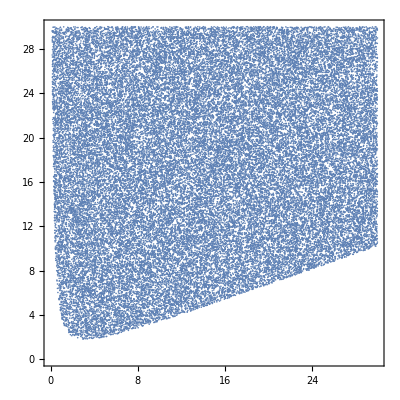

```mathematica
ListPlot[Drop[lmin12345,None,{3}],Frame->True,PlotLegends->Placed[legend,Right],AspectRatio->1,FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{0,30},{0,30}}]
```

```mathematica
Export["FixedPoints/EigenValuesDEAnI.pdf",lll];
```

```mathematica
ListContourPlot[ll1,Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{1}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],ColorFunction->"TemperatureMap",AspectRatio->1,FrameLabel->{MaTeX["\\alpha"],MaTeX["\\beta"]}]
```

```mathematica
ListContourPlot[ll2,Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{2}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],ColorFunction->"TemperatureMap",AspectRatio->1,FrameLabel->{MaTeX["\\alpha"],MaTeX["\\beta"]}]
```

```mathematica
ListContourPlot[ll3,Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{3}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],ColorFunction->"TemperatureMap",AspectRatio->1,FrameLabel->{MaTeX["\\alpha"],MaTeX["\\beta"]}]
```

```mathematica
ListContourPlot[ll4,Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{4}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],ColorFunction->"TemperatureMap",AspectRatio->1,FrameLabel->{MaTeX["\\alpha"],MaTeX["\\beta"]}]
```

```mathematica
ListContourPlot[ll5,Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{5}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],ColorFunction->"TemperatureMap",AspectRatio->1,FrameLabel->{MaTeX["\\alpha"],MaTeX["\\beta"]}]
```

```mathematica
L1 = {};
L2 = {};
L3 = {};
L4 = {};
L5 = {};
```

```mathematica
Do[
  np = 1;
  While[np<Length[EigenSystemNoViable[[i]]]&&AnyTrue[Sign[Re[EigenSystemNoViable[[i, np, 1]]]], # > 0 &], np++;];
  AppendTo[
   L1, {
SolNoViable[[i,1, 1]], SolNoViable[[i,1 ,2]],
 {
Re[EigenSystemNoViable[[i, np, 1, 1]]],EigenSystemNoViable[[i,np,2,1]]
}
}];
  AppendTo[
   L2, {
SolNoViable[[i,1, 1]], SolNoViable[[i,1 ,2]],
 {
Re[EigenSystemNoViable[[i, np, 1, 2]]],EigenSystemNoViable[[i,np,2,2]]
}
}];
  AppendTo[
   L3, {
SolNoViable[[i,1, 1]], SolNoViable[[i,1 ,2]],
 {
Re[EigenSystemNoViable[[i, np, 1, 3]]],EigenSystemNoViable[[i,np,2,3]]
}
}];
  AppendTo[
   L4, {
SolNoViable[[i,1, 1]], SolNoViable[[i,1 ,2]],
 {
Re[EigenSystemNoViable[[i, np, 1, 4]]],EigenSystemNoViable[[i,np,2,4]]}
}];
  AppendTo[
   L5, {
SolNoViable[[i,1, 1]], SolNoViable[[i,1 ,2]],
 {
Re[EigenSystemNoViable[[i, np, 1, 5]]],EigenSystemNoViable[[i,np,2,5]]}
}];
    , {i, 1, Length[SolNoViable]}] // AbsoluteTiming
```

{6.0502,Null}

Sign of eigen values depending on the α and β

```mathematica
Ll1=Table[{L1[[n,1]],L1[[n,2]],Sign@L1[[n,3,1]],L1[[n,3,2]]},{n,1,Length[L1]}];
Ll2=Table[{L2[[n,1]],L2[[n,2]],Sign@L2[[n,3,1]],L2[[n,3,2]]},{n,1,Length[L2]}];
Ll3=Table[{L3[[n,1]],L3[[n,2]],Sign@L3[[n,3,1]],L3[[n,3,2]]},{n,1,Length[L3]}];
Ll4=Table[{L4[[n,1]],L4[[n,2]],Sign@L4[[n,3,1]],L4[[n,3,2]]},{n,1,Length[L4]}];
Ll5=Table[{L5[[n,1]],L5[[n,2]],Sign@L5[[n,3,1]],L5[[n,3,2]]},{n,1,Length[L5]}];
```

```mathematica
Lmax12345=DeleteCases[Table[{L1[[n,1]],L1[[n,2]],Sign@Max[L1[[n,3,1]],L2[[n,3,1]],L3[[n,3,1]],L4[[n,3,1]],L5[[n,3,1]]]},{n,1,Length[L1]}],{_,_,-1}];
Lmin12345=DeleteCases[Table[{L1[[n,1]],L1[[n,2]],Sign@Min[L1[[n,3,1]],L2[[n,3,1]],L3[[n,3,1]],L4[[n,3,1]],L5[[n,3,1]]]},{n,1,Length[L1]}],{_,_,+1}];
```

```mathematica
Lll=ListPlot[{Drop[lmin12345,None,{3}],Drop[Lmin12345,None,{3}],Drop[Lmax12345,None,{3}]},Frame->True,PlotLegends->Placed[legend,Right],AspectRatio->1,PlotStyle->{Blue,Blue,Red},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{-30,30},{0,30}},Axes->False]
```

```mathematica
StabilityParameters=RegionPlot[{(α<0&&β<-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β>-α/3+2/3 √((36+α^4)/α^2)),(α<0&&β>-α/3-2/3 √((36+α^4)/α^2))||α==0||(α>0&&β<-α/3+2/3 √((36+α^4)/α^2))},{α,-5,30},{β,0,30},PlotStyle->{Blue,Red},PlotLegends->{Placed[legend,Right],Placed[Rotate[(MaTeX[#,Magnification->2.5]&)/@Style["\\lambda_{\\{1,2,3,4,5\\}}<0"],45°],{0.55,0.65}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["\\lambda_1>0||\\lambda_2>0||\\lambda_3>0||\\lambda_4>0||\\lambda_5>0"],90°],{0.1,0.5}],Placed[Rotate[(MaTeX[#,Magnification->1.4]&)/@Style["c_1\\hat{e}_x+c_2\\hat{e}_y+c_3\\hat{e}_z+c_4\\hat{e}_{\\Sigma}+c_5\\hat{e}_{\\Sigma}"],19°],{0.65,0.16}],Placed[Rotate[(MaTeX[#,Magnification->1.5]&)/@Style["c_3\\neq0\\neq c_4"],0°],{0.75,0.09}]},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]}]
```

-Graphics-

```mathematica
Export["FixedPoints/Stability.pdf",StabilityParameters];
```

```mathematica
ListPlot[{Drop[DeleteCases[Ll1,{_,_,+1,_}],None,{3,4}],Drop[DeleteCases[Ll1,{_,_,-1,_}],None,{3,4}]},Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{1}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],AspectRatio->1,PlotStyle->{Blue,Red},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{-30,30},{0,30}},Axes->False]
```

```mathematica
ListPlot[{Drop[DeleteCases[Ll2,{_,_,+1,_}],None,{3,4}],Drop[DeleteCases[Ll2,{_,_,-1,_}],None,{3,4}]},Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{2}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],AspectRatio->1,PlotStyle->{Blue,Red},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{-30,30},{0,30}},Axes->False]
```

```mathematica
ListPlot[{Drop[DeleteCases[Ll3,{_,_,+1,_}],None,{3,4}],Drop[DeleteCases[Ll3,{_,_,-1,_}],None,{3,4}]},Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{3}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],AspectRatio->1,PlotStyle->{Blue,Red},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{-30,30},{0,30}},Axes->False]
```

```mathematica
ListPlot[{Drop[DeleteCases[Ll4,{_,_,+1,_}],None,{3,4}],Drop[DeleteCases[Ll4,{_,_,-1,_}],None,{3,4}]},Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{4}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],AspectRatio->1,PlotStyle->{Blue,Red},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{-30,30},{0,30}},Axes->False]
```

```mathematica
ListPlot[{Drop[DeleteCases[Ll5,{_,_,+1,_}],None,{3,4}],Drop[DeleteCases[Ll5,{_,_,-1,_}],None,{3,4}]},Frame->True,PlotLegends->Placed[SwatchLegend[{RGBColor[0.2,0.3,1.],Red},{"-1","1"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->(MaTeX[#,Magnification->1.4]&)/@Style["\\text{sign}[\\lambda_{5}]"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right],AspectRatio->1,PlotStyle->{Blue,Red},FrameLabel->{(MaTeX[#,Magnification->1.4]&)/@Style["\\alpha"],(MaTeX[#,Magnification->1.4]&)/@Style["\\beta"]},PlotRange->{{-30,30},{0,30}},Axes->False]
```

```mathematica
EigenVectorL1=Table[
{{Ll1[[n,1]],Ll1[[n,2]]},
{Norm[Ll1[[n,4,1]]]Cos[Arg[Ll1[[n,4,1]]]],Norm[Ll1[[n,4,1]]]Sin[Arg[Ll1[[n,4,1]]]]},
{Norm[Ll1[[n,4,2]]]Cos[Arg[Ll1[[n,4,2]]]],Norm[Ll1[[n,4,2]]]Sin[Arg[Ll1[[n,4,2]]]]},
{Norm[Ll1[[n,4,3]]]Cos[Arg[Ll1[[n,4,3]]]],Norm[Ll1[[n,4,3]]]Sin[Arg[Ll1[[n,4,3]]]]},
{Norm[Ll1[[n,4,4]]]Cos[Arg[Ll1[[n,4,4]]]],Norm[Ll1[[n,4,4]]]Sin[Arg[Ll1[[n,4,4]]]]},
{Norm[Ll1[[n,4,5]]]Cos[Arg[Ll1[[n,4,5]]]],Norm[Ll1[[n,4,5]]]Sin[Arg[Ll1[[n,4,5]]]]}
},{n,1,Length[Ll1]}

];
EigenVectorL2=Table[
{{Ll2[[n,1]],Ll2[[n,2]]},
{Norm[Ll2[[n,4,1]]]Cos[Arg[Ll2[[n,4,1]]]],Norm[Ll2[[n,4,1]]]Sin[Arg[Ll2[[n,4,1]]]]},
{Norm[Ll2[[n,4,2]]]Cos[Arg[Ll2[[n,4,2]]]],Norm[Ll2[[n,4,2]]]Sin[Arg[Ll2[[n,4,2]]]]},
{Norm[Ll2[[n,4,3]]]Cos[Arg[Ll2[[n,4,3]]]],Norm[Ll2[[n,4,3]]]Sin[Arg[Ll2[[n,4,3]]]]},
{Norm[Ll2[[n,4,4]]]Cos[Arg[Ll2[[n,4,4]]]],Norm[Ll2[[n,4,4]]]Sin[Arg[Ll2[[n,4,4]]]]},
{Norm[Ll2[[n,4,5]]]Cos[Arg[Ll2[[n,4,5]]]],Norm[Ll2[[n,4,5]]]Sin[Arg[Ll2[[n,4,5]]]]}
},{n,1,Length[Ll2]}

];
EigenVectorL3=Table[
{{Ll3[[n,1]],Ll3[[n,2]]},
{Norm[Ll3[[n,4,1]]]Cos[Arg[Ll3[[n,4,1]]]],Norm[Ll3[[n,4,1]]]Sin[Arg[Ll3[[n,4,1]]]]},
{Norm[Ll3[[n,4,2]]]Cos[Arg[Ll3[[n,4,2]]]],Norm[Ll3[[n,4,2]]]Sin[Arg[Ll3[[n,4,2]]]]},
{Norm[Ll3[[n,4,3]]]Cos[Arg[Ll3[[n,4,3]]]],Norm[Ll3[[n,4,3]]]Sin[Arg[Ll3[[n,4,3]]]]},
{Norm[Ll3[[n,4,4]]]Cos[Arg[Ll3[[n,4,4]]]],Norm[Ll3[[n,4,4]]]Sin[Arg[Ll3[[n,4,4]]]]},
{Norm[Ll3[[n,4,5]]]Cos[Arg[Ll3[[n,4,5]]]],Norm[Ll3[[n,4,5]]]Sin[Arg[Ll3[[n,4,5]]]]}
},{n,1,Length[Ll3]}

];
EigenVectorL4=Table[
{{Ll4[[n,1]],Ll4[[n,2]]},
{Norm[Ll4[[n,4,1]]]Cos[Arg[Ll4[[n,4,1]]]],Norm[Ll4[[n,4,1]]]Sin[Arg[Ll4[[n,4,1]]]]},
{Norm[Ll4[[n,4,2]]]Cos[Arg[Ll4[[n,4,2]]]],Norm[Ll4[[n,4,2]]]Sin[Arg[Ll4[[n,4,2]]]]},
{Norm[Ll4[[n,4,3]]]Cos[Arg[Ll4[[n,4,3]]]],Norm[Ll4[[n,4,3]]]Sin[Arg[Ll4[[n,4,3]]]]},
{Norm[Ll4[[n,4,4]]]Cos[Arg[Ll4[[n,4,4]]]],Norm[Ll4[[n,4,4]]]Sin[Arg[Ll4[[n,4,4]]]]},
{Norm[Ll4[[n,4,5]]]Cos[Arg[Ll4[[n,4,5]]]],Norm[Ll4[[n,4,5]]]Sin[Arg[Ll4[[n,4,5]]]]}
},{n,1,Length[Ll4]}

];
EigenVectorL5=Table[
{{Ll5[[n,1]],Ll5[[n,2]]},
{Norm[Ll5[[n,4,1]]]Cos[Arg[Ll5[[n,4,1]]]],Norm[Ll5[[n,4,1]]]Sin[Arg[Ll5[[n,4,1]]]]},
{Norm[Ll5[[n,4,2]]]Cos[Arg[Ll5[[n,4,2]]]],Norm[Ll5[[n,4,2]]]Sin[Arg[Ll5[[n,4,2]]]]},
{Norm[Ll5[[n,4,3]]]Cos[Arg[Ll5[[n,4,3]]]],Norm[Ll5[[n,4,3]]]Sin[Arg[Ll5[[n,4,3]]]]},
{Norm[Ll5[[n,4,4]]]Cos[Arg[Ll5[[n,4,4]]]],Norm[Ll5[[n,4,4]]]Sin[Arg[Ll5[[n,4,4]]]]},
{Norm[Ll5[[n,4,5]]]Cos[Arg[Ll5[[n,4,5]]]],Norm[Ll5[[n,4,5]]]Sin[Arg[Ll5[[n,4,5]]]]}
},{n,1,Length[Ll5]}

];
```